## Setup

```mathematica
SetDirectory["/Volumes/marshallShare/YK_Alt_Kernels/"]
ix=3;
rawFine=Import["Fine_y"<>ToString[ix]<>"k.csv"];
```

/Volumes/marshallShare/YK_Alt_Kernels

## Check

## Fine

```mathematica
Length[rawFine]
matrix=MatrixPlot[rawFine
,ColorFunction->(Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{0,Directive[RGBColor[1, 1, 1],Opacity[0]]},{-1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,Frame->None
,FrameStyle->None
,FrameTicks->None
,ImagePadding->None
,ImageSize->1000
,PlotRange->{{0,All},{0,All},{-1,1}}
,PlotRangePadding->0
];
Export[NotebookDirectory[]<>"images/YK2.pdf",matrix]
```

923

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/DataAnalysis/KernelsComparison/images/YK2.pdf

```mathematica
kernel=rawFine;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
(*MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];*)
markovPDFFine=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
```

## Coarse

```mathematica
raw=Import["YorkeysKnob_02.csv"];
Length[raw]
```

923

```mathematica
rawCoarse=Import["YorkeysKnob_02Kernel.csv"][[2;;All,2;;All]];
Length[rawCoarse]
matrix=MatrixPlot[Chop[rawCoarse,10^-4]
,ColorFunction->(Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{0,Directive[RGBColor[1, 1, 1],Opacity[0]]},{-1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,Frame->None
,FrameStyle->None
,FrameTicks->None
,ImagePadding->None
,ImageSize->1000
,PlotRange->{{0,All},{0,All},{-1,1}}
,PlotRangePadding->0
];
```

923

```mathematica
kernel=rawCoarse;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
(*MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];*)
markovPDFCoarse=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
```

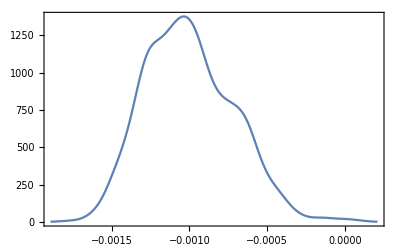

```mathematica
SmoothHistogram[markovPDF-markovPDFFine
,Frame->True
,FrameStyle->Thick
]
```

## Difference

```mathematica
diff=rawCoarse-rawFine;
range={-.01,.01};
matrix=MatrixPlot[diff
,Background->None
,ColorFunction->(Blend[{{range[[1]],Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1]]},{0,Directive[RGBColor[1, 1, 1],Opacity[.5]]},{range[[2]],Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,Frame->None
,FrameStyle->None
,FrameTicks->None
,ImagePadding->None
,ImageSize->1000
,PlotRange->{{0,All},{0,All},{-1,1}}
,PlotRangePadding->0
,PlotLegends->Automatic
];
Export[NotebookDirectory[]<>"images/"<>ToString[ix]<>"M.png",matrix,ImageSize->2500,ImageResolution->250]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/DataAnalysis/KernelsComparison/images/3M.png

```mathematica
rx={1,10}
{min,max}={diff//Flatten//Min,diff//Flatten//Max};
colors=Prepend[Blend[{{rx[[1]],Directive[RGBColor[1, 0., 0.9347219043259327],Opacity[.1]]},{rx[[2]],Directive[RGBColor[0, 0, 1],Opacity[.1]]}},#]&/@Range[rx[[1]],rx[[2]]],Directive[Red,Opacity[.1]]];
scatter=Table[
ListPlot[Diagonal[diff,i-1]//Abs
,Frame->True
,FrameLabel->(Style[#,50]&/@{"ID","Probability Difference"})
,FrameStyle->Directive[Thick,Opacity[.75]]
,FrameTicksStyle->20
,ImageSize->1250
,PlotRange->{{0,All},{0,.1}}
,PlotStyle->colors[[i]]
]
,{i,rx[[1]],rx[[2]]}]//Show;
Export[NotebookDirectory[]<>"images/"<>ToString[ix]<>"S.png",scatter,ImageSize->2500]
```

{1,10}

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/DataAnalysis/KernelsComparison/images/3S.png

{0,10}

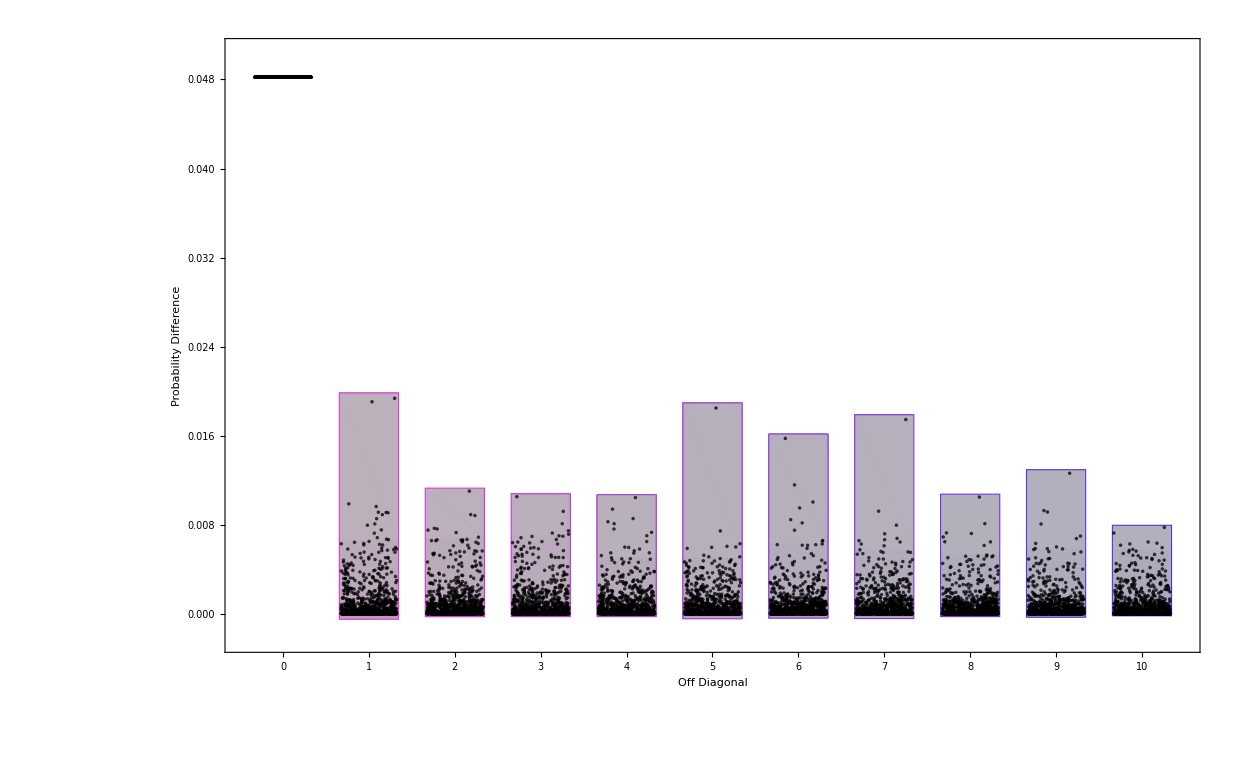

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/DataAnalysis/KernelsComparison/images/3D.png

```mathematica
rx={0,10}
{min,max}={diff//Flatten//Min,diff//Flatten//Max};
colors=Prepend[Blend[{{rx[[1]],Directive[RGBColor[1, 0., 0.9347219043259327],EdgeForm[White],Opacity[.75]]},{rx[[2]],Directive[RGBColor[0, 0, 1],Opacity[.75]]}},#]&/@Range[rx[[1]],rx[[2]]],Directive[Red,Opacity[.65]]];
dist=DistributionChart[Abs[Diagonal[diff,#]&/@Range[rx[[1]],rx[[2]]]]
,ChartStyle->colors
,ChartLabels->Range[rx[[1]],rx[[2]]]
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Off Diagonal","Probability Difference"})
,FrameStyle->Directive[Thick,Opacity[.75]]
,FrameTicksStyle->20
,ImageSize->1250
,PlotRange->{{-.05,All},{0,.1}}
,ChartElementFunction->ChartElementData["PointDensity",PlotStyle->Opacity[.5]]
]
Export[NotebookDirectory[]<>"images/"<>ToString[ix]<>"D.png",dist,ImageSize->2500]
```